```mathematica
(*Початоква купа формул*)
ClearAll[x,t]
G:=(-Log[x^2+t^2]/Pi)/.{x->(x-xI),t->(t-tI)}
G:=(x^2+t^2)/.{x->(x-xI),t->(t-tI)}
G
u := -1/5*Sin[x/5]-1/4*Cos[t/4]
uI:=u/.{x->xI,t->tI}
y:=5*Sin[x/5]+4Cos[t/4]
(*Просторово-часова область*)
t1:=0
t2:=50
x1:=0
x2:=50
T:={t,t1,t2}
TI:=T/.{t->tI}
X:={x,x1,x2}
XI:=X/.{x->xI}
```

(t-tI)^2+(x-xI)^2

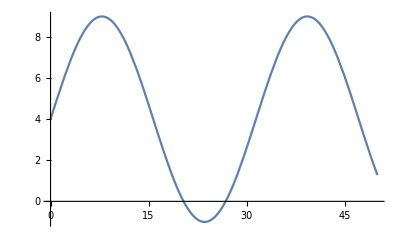

```mathematica
(*Початкові умови*)
Plot[y/.{t->t1},Evaluate[X]]
```

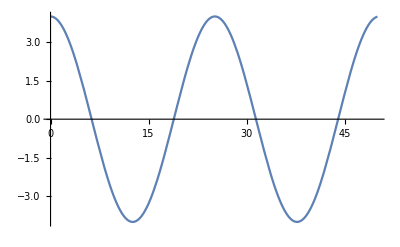

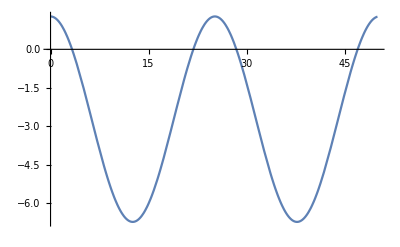

```mathematica
(*Крайові умови*)
Plot[y/.{x->x1},Evaluate[T]]
Plot[y/.{x->x2},Evaluate[T]]
```

```mathematica
(*Перший у*)
(*yInf=Re[N[Integrate[G*u,Evaluate[X],Evaluate[T]]]]*)
yInf:=Integrate[G*uI,Evaluate[XI],Evaluate[TI]]
yInf
```

50/3 (-2350-24 t-3 (-50+t) t-3 x^2+(2350+3 (-50+t) t+3 (-50+x)^2) Cos[10]-1200 Cos[25/2]+24 t Cos[25/2]+30 (-50+x) Sin[10]-(9904+3 (-100+t) t+3 (-50+x) x) Sin[25/2])

```mathematica
(*B11y:=N[Integrate[G*y/.{t->t1},Evaluate[X]]]
B21y:=N[Integrate[G*y/.{x->x1},Evaluate[T]]]+N[Integrate[G*y/.{x->x2},Evaluate[T]]]
B12y:=B11y
B22y=B21y
By1:=B11y+B12y
By2:=B21y+B22y*)
(*Точки для подбудови вектори U*)
m0:={{xI->1,tI->-10},{xI->2,tI->-20},{xI->3,tI->-30},{xI->4,tI->-1},{xI->5,tI->-2}}
mE:={{xI->100,tI->1},{xI->200,tI->30},{xI->55,tI->10},{xI->65,tI->20},{xI->75,tI->30}}
(*Вектори В*)
B11:=G/.m0/.{t->0}
B12:=G/.mE/.{t->0}
B21:=G/.m0
B22:=G/.mE
```

```mathematica
(*Вектори Ву*)
By1:=Total[Integrate[B11*y,Evaluate[X]]][[1]]+Total[Integrate[B21*y,Evaluate[T]]/.{x->{x2-x1}}][[1]]
By2:=Total[Integrate[B12*y,Evaluate[X]]][[1]]+Total[Integrate[B22*y,Evaluate[T]]/.{x->{x2-x1}}][[1]]
```

-8064+40064 Cos[25/2]+(14832500 Sin[10])/3+50/3 (531-3981 Cos[10]+13648 Cos[t/4]+720 Sin[10])+497600 Sin[25/2]